```mathematica
path=NotebookDirectory[];
datafiles=FileNames[FileNameJoin@{path,"rabi*.csv"}]
```

{/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_20190217/rabi_Omega100_bangramp_neldermead.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_20190217/rabi_Omega100_bangramp_powell.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_20190217/rabi_Omega100_crab_10freq_neldermead.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_20190217/rabi_Omega100_crab_10freq_powell.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_20190217/rabi_Omega100_crab_2freq_neldermead.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_20190217/rabi_Omega100_crab_2freq_powell.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_20190217/rabi_Omega100_crab_3freq_neldermead.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_20190217/rabi_Omega100_crab_3freq_powell.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_20190217/rabi_Omega100_doublebang_neldermead.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_20190217/rabi_Omega100_doublebang_powell.csv}

```mathematica
bangRampParametersToProtocol[tf_,y0_,t1_,y1_,y2_]:=Piecewise[{{y0,0≤t≤t1},{(y2-y1)(t-t1)/(tf-t1)+y1,t1<t≤tf}}];
doubleBangParametersToProtocol[tf_,y0_,t1_,y1_]:=Piecewise[{{y0,0≤t≤t1},{y1,t1<t≤tf}}];
CRABParametersToProtocol[tf_,frequencies_,Ak_,Bk_,y0_,y1_]:=Module[{baseline,normalisingPulse,pulseCorrection,finalProtocol},
normalisingPulse[t_]:=0.1 t (t-tf);
pulseCorrection[t_]:=1+normalisingPulse[t]*Total@Plus[
Ak*Sin[frequencies*t],
Bk*Cos[frequencies*t]
];
baseline[t_]:=Interpolation[{{0,y0},{tf,y1}},InterpolationOrder->1][t];
finalProtocol[t_]:=baseline[t]*pulseCorrection[t];
finalProtocol[t]
];
protocolFromDatafile[data_,filename_]:=Which[
StringCases[filename,"bangramp"]≠{},
bangRampParametersToProtocol@@data⟦{1,3,4,5,6}⟧,
StringCases[filename,"doublebang"]≠{},
doubleBangParametersToProtocol@@data⟦{1,3,4,5}⟧,
StringCases[filename,"crab"]≠{},
With[{criticalParValue=Which[
StringContainsQ[filename,"rabi"],5,
StringContainsQ[filename,"lmg"],1
]},
CRABParametersToProtocol@@Join[{data⟦1⟧},Partition[data⟦3;;⟧,Length@data⟦3;;⟧/3],{0,criticalParValue}]
]
];
```

```mathematica
First@Select[datafiles,StringContainsQ[#,"crab_10freq"]&]
```

/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_20190217/rabi_Omega100_crab_10freq_neldermead.csv

```mathematica
(fooData=Import[First@Select[datafiles,StringContainsQ[#,"crab_10freq"]&]]⟦1;;20,All⟧)//TableForm
```

| tf | fid | nu0 | nu1 | nu2 | nu3 | nu4 | nu5 | nu6 | nu7 | nu8 | nu9 | A0 | A1 | A2 | A3 | A4 | A5 | A6 | A7 | A8 | A9 | B0 | B1 | B2 | B3 | B4 | B5 | B6 | B7 | B8 | B9
0 | 0.1 | 0.762725 | 0.000283773 | -0.00335809 | -0.00351348 | 0.00169203 | -0.00311488 | 0.00376861 | 0.00436184 | 0.00449076 | 0.0019702 | -0.000489436 | -0.911864 | 1.02653 | 1.30237 | -0.75541 | -0.850787 | -0.358696 | -0.819158 | 6.06525 | -0.906973 | -0.862284 | -7.2311 | -0.876118 | -1.64132 | -2.36801 | -15.7149 | -0.0250435 | 0.609447 | 0.719644 | -0.152674 | 0.00882032
1 | 0.139394 | 0.762927 | -0.0039297 | 0.00209612 | -0.000902684 | 0.00200786 | -0.00356492 | 0.000671587 | -0.00492161 | -0.00659709 | -0.00546973 | 0.00662124 | 0.0617546 | 2.4188 | 0.856418 | -0.594988 | 0.766496 | 0.877807 | 1.67617 | 0.205225 | -0.849706 | -0.00867717 | 0.0145713 | 0.624805 | -4.84878 | 0.281095 | -0.694848 | -2.55352 | -0.880981 | -0.0590565 | -0.500441 | -0.375316
2 | 0.178788 | 0.763975 | -0.00837891 | 0.00599468 | 0.0039538 | 0.00402618 | -0.00807459 | 0.00333483 | 0.00121981 | 0.00753172 | -0.00840258 | 0.00853495 | -57.4083 | -2575.41 | 478.226 | 13619.2 | -1731.74 | 5096.65 | 1944.95 | 2438.23 | -8874.1 | 131.209 | 70.4335 | -464.957 | -757.425 | -789.008 | 48.7636 | -832.634 | -274.718 | -4732.85 | 2161.23 | 503.715
3 | 0.218182 | 0.764747 | 0.00604625 | -0.00647501 | -0.000363511 | 0.0062487 | 0.00279544 | 0.000155552 | -0.0101772 | 0.000404227 | 0.00751049 | -0.00310051 | -16052. | 839.156 | -15251.9 | 10138.8 | 10624.6 | 76.7594 | -7847.66 | 5675.47 | 162.407 | -2721.67 | 12812.4 | -2489.23 | -2713.94 | 27422.4 | -5588.76 | -8433.68 | -773.529 | -11389. | 2245.01 | -15030.8
4 | 0.257576 | 0.767184 | 0.0128203 | 0.0113195 | -0.00151804 | 0.0115965 | -0.00435498 | 0.00978049 | 0.0122567 | -0.00321802 | -0.00841278 | 0.00119182 | -137.081 | -602.048 | -126.261 | 354.553 | 37.7137 | 2574.99 | 10064.4 | -482.271 | -549.6 | 179.721 | 1.78728 | 108.792 | -2008.28 | -1215.13 | -4291.51 | -75.4383 | -87.4588 | -300.191 | 5318.44 | -1377.48
5 | 0.29697 | 0.768872 | -0.0132094 | 0.00609044 | 0.00157917 | -0.00986413 | 0.0070554 | 0.0102409 | 0.00412933 | 0.00724572 | -0.0137995 | -0.00547799 | -152.694 | -669.356 | 384.906 | -15.4014 | 763.271 | 420.894 | -267.509 | 2038.93 | -4869.88 | -314.675 | -378.917 | -408.352 | -315.424 | 67.0459 | -546.273 | 6.78466 | -440.488 | -895.616 | 115.226 | -163.731
6 | 0.336364 | 0.770834 | 0.0167251 | 0.0127503 | -0.0168054 | 0.0135677 | -0.0113836 | 0.0141767 | -0.0152987 | 0.0113171 | 0.0135981 | -0.00812532 | -243.066 | -400.512 | -785.696 | 59.5502 | -3164.44 | 753.825 | 540.443 | 1089.87 | -770.809 | -3968.84 | -310.121 | -482.559 | -3.21127 | 803.682 | 0.201694 | -848.817 | -13.2019 | 409.29 | -200.484 | -1553.29
7 | 0.375758 | 0.773504 | 0.00891799 | -0.00607578 | 0.0128952 | -0.0089124 | -0.0128934 | 0.0170624 | -0.00872399 | 0.0157153 | -0.00819499 | 0.00744266 | -49.1294 | 582.341 | -755.665 | -200.016 | -566.019 | 975.519 | -4550.02 | 129.607 | -229.593 | 87.8354 | 250.536 | -382.088 | -62.2206 | 80.943 | -23.6316 | -22.941 | -221.483 | -1178.9 | -212.782 | -3.57029
8 | 0.415152 | 0.776716 | 0.00901343 | -0.0185483 | -0.00480602 | 0.012392 | 0.00446963 | -0.00790564 | 0.0160967 | 0.00271165 | 0.00541231 | 0.00450702 | 917.383 | 982.975 | -60.0259 | 6353.31 | 1322.23 | -118.267 | 1154.07 | 2965.93 | 171. | 93.7543 | -520.954 | 1798.13 | -355.647 | -86.5515 | -908.249 | -561.339 | 2418.95 | -2377.19 | -582.064 | -620.934
9 | 0.454545 | 0.779463 | -0.0184231 | -0.00148211 | 0.0185443 | 0.0203277 | 0.00801735 | -0.0114141 | -0.0142931 | -0.0163673 | 0.00184615 | -0.00276283 | -94.7106 | -53.0419 | -5.75769 | 114.577 | 266.182 | 350.789 | -2633.14 | -778.725 | 30.7661 | 81.9224 | -1126.89 | 85.2025 | -124.552 | -168.292 | -43.7355 | 306.366 | -314.424 | -30.4667 | 41.6892 | 3.24902
10 | 0.493939 | 0.78266 | 0.0145624 | 0.0143092 | -0.00712398 | -0.00863023 | 0.00714635 | 0.0127806 | -0.00621298 | 0.0206593 | -0.0136193 | 0.011255 | 740.175 | -182.917 | -6.21634 | -344.525 | -92.8934 | 287.639 | 0.500603 | 200.723 | -1540.98 | 262.698 | -119.382 | 144.446 | 129.97 | -420.084 | -137.888 | 20.3677 | -88.6216 | -76.9559 | -47.8366 | -541.285
11 | 0.533333 | 0.785333 | 0.0122002 | -0.000366624 | -0.0146449 | 0.000416154 | 0.0133549 | 0.0153432 | -0.00494137 | -0.0215811 | 0.0073387 | -0.0224501 | -556.364 | -51.1602 | -1016.15 | 958.133 | 283.393 | 161.467 | -836.988 | -518.63 | 75.257 | 80.2559 | 265.435 | 144.126 | -103.162 | 357.581 | -114.605 | -749.106 | -19.1905 | -72.172 | -272.691 | -290.018
12 | 0.572727 | 0.794337 | -0.0241015 | 0.00410253 | 0.025537 | -0.0129314 | 0.0161457 | 0.011527 | 0.0238751 | -0.0238826 | -0.000769559 | -0.00775306 | 2599.31 | 5850.99 | 1363.48 | -693.141 | -44.7006 | 433.285 | 3593.79 | -100.316 | 331.83 | 492.761 | -2970.57 | -1705.34 | -914.649 | -4632.23 | -164.647 | 100.023 | -1026.56 | 3013.85 | -1658.43 | 8215.58
13 | 0.612121 | 0.793778 | 0.0235706 | -0.0037031 | -0.0178253 | -0.0105799 | -0.0166131 | -0.0116763 | -0.0209679 | 0.0206649 | -0.0245958 | -0.0130885 | 45.2027 | -351.414 | 25.3181 | -39.1177 | 88.2296 | 21.8197 | 1.64745 | -85.0263 | -773.793 | -22.7966 | 112.262 | 67.8131 | 82.2353 | 154.911 | -24.4976 | -104.798 | -509.169 | -221.603 | -178.028 | -93.8158
14 | 0.651515 | 0.804147 | -0.00576202 | -0.0147503 | -0.00285306 | -0.0319929 | -0.00146965 | 0.0288001 | 0.0207129 | -0.0142429 | -0.00242916 | -0.0188732 | 625.583 | -2535.77 | -772.29 | -3291.46 | -333.369 | 206.297 | 108.014 | -292.431 | -1769.44 | -11.9058 | 15.1121 | -2256.81 | -886.835 | -231.309 | -1575.36 | 3729.39 | 223.193 | -379.58 | -306.287 | 241.444
15 | 0.690909 | 0.802985 | -0.0100447 | -0.0238864 | 0.0299733 | 0.0292286 | 0.0127495 | 0.0061479 | 0.00191044 | 0.0198401 | 0.00204619 | 0.0109941 | -15.8118 | -46.5159 | -25.0418 | 73.2438 | -2.60589 | 130.458 | -155.011 | 420.442 | -6.50139 | 753.14 | 57.0142 | -75.9094 | 110.731 | -95.218 | -221.212 | -284.305 | -77.4083 | -86.2757 | 50.7272 | 6.05292
16 | 0.730303 | 0.814275 | 0.0238578 | 0.0210613 | -0.00957787 | -0.0080173 | -0.023928 | -0.0275847 | -0.0345508 | -0.000178399 | 0.0249633 | 0.0347022 | 5.37759 | 774.599 | -354.68 | 27.8279 | 123.047 | -184.195 | -458.119 | 110.512 | 532.717 | 373.403 | -53.6463 | -1441.7 | 15.9267 | -221.56 | -368.605 | 917.014 | 1217.78 | 243.507 | -1579.33 | 211.004
17 | 0.769697 | 0.820411 | 0.0350377 | -0.0308492 | 0.0146253 | 0.030563 | 0.0157238 | -0.00999167 | 0.0010407 | 0.0304318 | 0.0255994 | -0.0250382 | -21.7381 | -711.787 | 627.765 | 169.234 | 26.9993 | -405.937 | 21.0581 | 758.975 | -393.946 | -818.438 | -41.1942 | -265.172 | -296.227 | -206.778 | 88.1602 | -961.181 | -148.007 | -160.429 | -889.313 | 1878.89
18 | 0.809091 | 0.815848 | -0.0227431 | 0.00155141 | -0.00171173 | 0.00710583 | -0.0179507 | 0.0167192 | 0.0246218 | -0.000177359 | 0.0143486 | 0.0124769 | -155.448 | 84.8779 | 64.2905 | 438.401 | -48.8701 | 200.842 | 110.616 | -144.947 | 105.335 | 26.4794 | -144.573 | 26.0367 | 793.069 | -61.5699 | -429.967 | 173.754 | -34.5463 | -161.18 | -536.481 | 0.0128289

```mathematica
fooData⟦12,4;;13⟧
```

{0.0145624,0.0143092,-0.00712398,-0.00863023,0.00714635,0.0127806,-0.00621298,0.0206593,-0.0136193,0.011255}

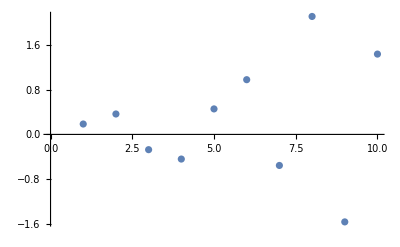

```mathematica
With[{idx=12},
2Pi Range[10]fooData⟦idx,4;;13⟧/fooData⟦idx,2⟧
]//ListPlot
```

```mathematica
DynamicModule[{datafiles=FileNames[FileNameJoin@{path,"rabi*.csv"}]},
Manipulate[
With[{filename=FileBaseName@datafiles⟦k⟧,data=Import[datafiles⟦k⟧]⟦2;;,2;;⟧},
GraphicsRow[{
ListPlot[data⟦All,2⟧,PlotRange->All,Joined->True,PlotMarkers->Automatic,
Epilog->{Red,PointSize@0.02,Point@{{solutionIndex,data⟦All,2⟧⟦solutionIndex⟧}}}
],
Plot[protocolFromDatafile[data⟦solutionIndex,All⟧,filename],{t,0,data⟦solutionIndex,1⟧},
PlotRange->{{0,4},All},PlotLabel->"total time:"<>ToString@data⟦solutionIndex,1⟧
]
},ImageSize->800,PlotLabel->filename]
],
(*{{k,1},1,Length@datafiles,1,Appearance->"Labeled"},*)
{{k,1},Thread[Range[Length@datafiles]->FileBaseName/@datafiles]},
{{solutionIndex,1},1,Length@Import[datafiles⟦k⟧]⟦2;;,2;;⟧,1,Appearance->"Labeled"},ControlPlacement->Right
]]
```

Part::partw: Part 1 of {} does not exist.

Import::chtype: First argument {}⟦1⟧ is not a valid file, directory, or URL specification.

Part::take: Cannot take positions 2 through -1 in $Failed.

Part::partd: Part specification $Failed⟦2;;All,2;;All⟧⟦All,2⟧ is longer than depth of object.

ListPlot::lpn: $Failed⟦2;;All,2;;All⟧⟦All,2⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦2;;All,2;;All⟧⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Plot::plln: Limiting value $Failed⟦2;;All,2;;All⟧⟦1,1⟧ in {Charting`Private`pvar$4139,0,$Failed⟦2;;All,2;;All⟧⟦1,1⟧} is not a machine-sized real number.

Plot::plln: Limiting value $Failed⟦2;;All,2;;All⟧⟦1,1⟧ in {Charting`Private`pvar$4169,0,$Failed⟦2;;All,2;;All⟧⟦1,1⟧} is not a machine-sized real number.

Plot::plln: Limiting value $Failed⟦2;;All,2;;All⟧⟦1,1⟧ in {Charting`Private`pvar$4210,0,$Failed⟦2;;All,2;;All⟧⟦1,1⟧} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

```mathematica
DynamicModule[{datafiles=FileNames[FileNameJoin@{path,"lmg*.csv"}]},
Manipulate[
With[{filename=FileBaseName@datafiles⟦k⟧,data=Import[datafiles⟦k⟧]⟦2;;,2;;⟧},
GraphicsRow[{
ListPlot[data⟦All,2⟧,PlotRange->All,Joined->True,PlotMarkers->Automatic,
Epilog->{Red,PointSize@0.02,Point@{{solutionIndex,data⟦All,2⟧⟦solutionIndex⟧}}}
],
Plot[protocolFromDatafile[data⟦solutionIndex,All⟧,filename],{t,0,data⟦solutionIndex,1⟧},
PlotRange->{{0,1},All},PlotLabel->"total time:"<>ToString@data⟦solutionIndex,1⟧
]
},ImageSize->800,PlotLabel->filename]
],
(*{{k,1},1,Length@datafiles,1,Appearance->"Labeled"},*)
{{k,1},Thread[Range[Length@datafiles]->FileBaseName/@datafiles]},
{{solutionIndex,1},1,Length@Import[datafiles⟦k⟧]⟦2;;,2;;⟧,1,Appearance->"Labeled"},ControlPlacement->Right
]]
```